```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize-> 14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
SetOptions[BarLegend,LabelStyle->{Black,FontSize->12,FontFamily->"Times"}];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],Scaled@{.016,0}}&/@(10^Range[-30,30,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,30,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,30,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,30,1])*#&/@Range[2,9,1]]];
logticksx3=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,30,5]),{Log10@#,"",{.008,0}}&/@(10^Range[-30,30,1])];
logticksx4=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,30,5]),{Log10@#,"",{.008,0}}&/@(10^Range[-30,30,1])];
logticksx5=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.005,0}}&/@(10^Range[-30,30,1]),{Log10@#,"",{.0015,0}}&/@Flatten[(10^Range[-30,30,1])*#&/@Range[2,9,1]]];
logticksx6=Join[{Log10@#,"",{.005,0}}&/@(10^Range[-30,30,1]),{Log10@#,"",{.0015,0}}&/@Flatten[(10^Range[-30,30,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript[Style["M",Italic],"⊙"],FormatType->StandardForm];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Constraints for monochromatic PBH mass functions

```mathematica
(* 0912.5297 *)
BBN = Import["BBN.dat"];
(* 2002.00898 *)
CMB = Import["CMB.dat"];
(* 0912.5297 *)
EGR = Import["EGR.dat"];
(* 1807.03075 *)
Voyager = Import["Voyager.dat"];
(* 1910.01285 *)
SUB = Import["SUB.dat"];
(* 1307.5798 *)
Kepler = Import["Kepler.dat"];
(* 0011506 *)
MACHO = Import["MACHO.dat"];
(* 0607207 *)
EROS = Import["EROS.dat"];
(* 2403.02386 *)
OGLE = Import["OGLE.dat"];
(* 1605.03665 *)
Eridanus = Import["Eridanus.dat"];
(* 1704.01668 *)
Segue1 = Import["Segue1.dat"];
(* 1712.02240 *)
SNe = Import["SNe.dat"];
(* 1406.5169 *)
WB = Import["WB.dat"];
(* 1705.00791 *)
xray = Import["xray.dat"];
(* 2405.05732 *)
LIGO = Import["LIGO.dat"];
(* 2303.17601 *)
LIGOlens = Import["LIGOlens.dat"];
(* 1903.10509 *)
Lya = Import["Lya.dat"];
(* 2002.10771 *)
acc = Import["acc.dat"];
```

```mathematica
interpolate[log10m_,list_]:=Piecewise[{{Interpolation[list,InterpolationOrder->1][log10m],First@First@list<log10m<First@Last@list}},100]
BBNf[log10m_] = interpolate[log10m,BBN];
CMBf[log10m_] = interpolate[log10m,CMB];
EGRf[log10m_] = interpolate[log10m,EGR];
Voyagerf[log10m_] = interpolate[log10m,Voyager];
SUBf[log10m_] = interpolate[log10m,SUB];
Keplerf[log10m_] = interpolate[log10m,Kepler];
MACHOf[log10m_] = interpolate[log10m,MACHO];
EROSf[log10m_] = interpolate[log10m,EROS];
OGLEf[log10m_] = interpolate[log10m,OGLE];
Eridanusf[log10m_] = interpolate[log10m,Eridanus];
Segue1f[log10m_] = interpolate[log10m,Segue1];
SNef[log10m_] = interpolate[log10m,SNe];
WBf[log10m_] = interpolate[log10m,WB];
xrayf[log10m_] = interpolate[log10m,xray];
LIGOf[log10m_] = interpolate[log10m,LIGO];
LIGOlensf[log10m_] = interpolate[log10m,LIGOlens];
Lyaf[log10m_] = interpolate[log10m,Lya];
accf[log10m_] = interpolate[log10m,acc];
```

```mathematica
Mevap = 2.55*^-19;
```

```mathematica
ColorData[97,"ColorList"][[1]]
```

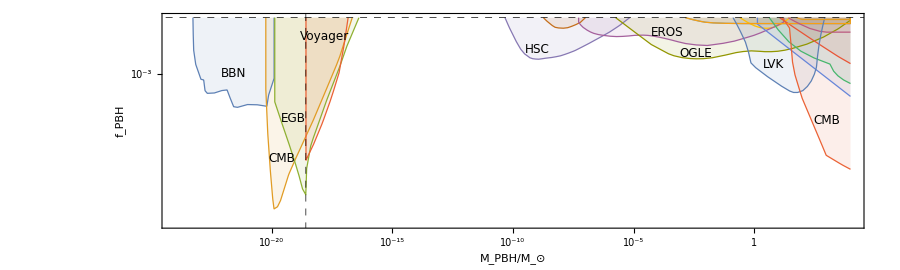

```mathematica
Show[Plot[{BBNf[x],CMBf[x],EGRf[x],Voyagerf[x],SUBf[x],Keplerf[x],SNef[x],MACHOf[x],EROSf[x],OGLEf[x],Eridanusf[x],Segue1f[x],SNef[x],WBf[x],xrayf[x],LIGOf[x],LIGOlensf[x],Lya[x],accf[x]},{x,-24,4},Filling->Top,PlotStyle->Thickness[0.001],FillingStyle->Opacity[0.1],PlotRange->{{-24,4},{-11,0}},PlotRangePadding->None,GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Black, Dashed],FrameLabel->{"M_PBH/"<>Msunt,"f_PBH"},AspectRatio->0.3,ImageSize->900,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{logticksx5,logticksx6},{logticksx5,logticksx6}},ImagePadding->{{58,10},{42,10}}],
Graphics[Text[Rotate[Style["BBN",12],0Degree],{-21.6,-3.}]],
Graphics[Text[Rotate[Style["CMB",12],0Degree],{-19.6,-7.5}]],
Graphics[Text[Rotate[Style["EGB",12],0Degree],{-19.1,-5.4}]],
Graphics[Text[Rotate[Style["Voyager",12],0Degree],{-17.8,-1.}]],Graphics[Text[Rotate[Style["HSC",12],0Degree],{-9.,-1.7}]],
Graphics[Text[Rotate[Style["EROS",12],0Degree],{-3.6,-0.8}]],
Graphics[Text[Rotate[Style["OGLE",12],0Degree],{-2.4,-1.9}]],
Graphics[Text[Rotate[Style["LVK",12],0Degree],{0.8,-2.5}]],
Graphics[Text[Rotate[Style["CMB",12],0Degree],{3.,-5.5}]]]
```

## Constraints for critical collapse mass functions

```mathematica
constr[ψ_,constrf_,logm1_,logm2_]:=NIntegrate[Log[10]10^logm ψ[10^logm]/10^constrf[logm],{logm,logm1,logm2}]
```

{n→c^(1+1/γ)/Gamma[1+1/γ]}

{c→Gamma[2+1/γ]/Gamma[1+1/γ]}

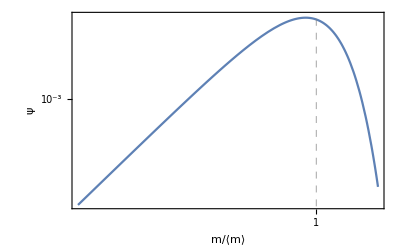

```mathematica
ψ[mavg_]=n(#/mavg)^(1+1/γ)/# Exp[-c(#/mavg)]&;
nsol = First@Solve[1==Integrate[ψ[mavg][m],{m,0,Infinity},Assumptions->{mavg>0,c>0,n>0,γ>0}],n]
csol = First@Solve[mavg ==Integrate[m ψ[mavg][m],{m,0,Infinity},Assumptions->{mavg>0,c>0,n>0,γ>0}]/.nsol,c]
ψ[mavg_] = ψ[mavg]/.nsol/.csol/.γ->0.36;
Plot[Log10@ψ[1][10^x],{x,-3,Log10@6},FrameLabel->{"m/⟨m⟩","ψ"},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},GridLines->{{0},{}},GridLinesStyle->Directive[Gray, Dashed]]
```

```mathematica
AbsoluteTiming[clist = ParallelMap[{#,
Quiet@{constr[ψ[10^#],accf,0,5],
constr[ψ[10^#],OGLEf,-8,5],
constr[ψ[10^#],EROSf,-8,5],
constr[ψ[10^#],SUBf,-11,-3],
constr[ψ[10^#],LIGOf,-2,5],
constr[ψ[10^#],BBNf,-25.,-14.],
constr[ψ[10^#],CMBf,-25.,-14.],
constr[ψ[10^#],EGRf,-25.,-14.],
constr[ψ[10^#],Voyagerf,-25.,-15.]}}&,
Table[M,{M,-24,4.4,0.2}]];][[1]]/60.
```

0.1615

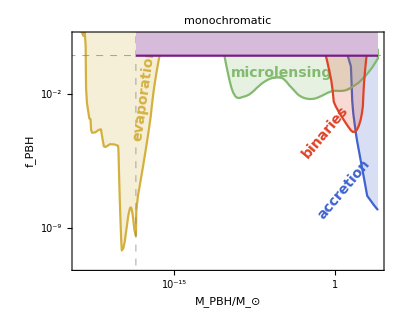

```mathematica
Show[Plot[accf[x],{x,0,4},PlotRange->{{-24,4},{-11,1}},Filling->Top,PlotStyle->ColorData["Rainbow"][0.2],PlotRangePadding->None,ImagePadding->{{58,4},{42,10}},GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"M_PBH/"<>Msunt,"f_PBH"},FrameTicks->{{logticksx,logticksx2},{logticksx3,logticksx4}},AspectRatio->0.8,ImageSize->400],
Plot[Log10[1/(1/10^SUBf[x]+1/10^EROSf[x]+1/10^OGLEf[x])],{x,-11,4},Filling->Top,PlotStyle->{ColorData["Rainbow"][0.5],None}],
Plot[LIGOf[x],{x,-2,4},Filling->Top,PlotStyle->ColorData["Rainbow"][0.95]],
Plot[Log10[1/(1/10^BBNf[x]+1/10^CMBf[x]+1/10^EGRf[x]+1/10^Voyagerf[x])],{x,-24,-15},Filling->Top,PlotStyle->{ColorData["Rainbow"][0.72],None}],
Plot[0,{x,Log10@Mevap,4},PlotRange->{All,{-11,4}},Filling->Top,PlotStyle->ColorData["Rainbow"][0.],FillingStyle->Opacity[1,Lighter[ColorData["Rainbow"][0.],0.7]]],
Graphics[Text[Rotate[Style["evaporation",14,Bold,ColorData["Rainbow"][0.72]],82Degree],{-17.8,-2.}]],
Graphics[Text[Rotate[Style["microlensing",14,Bold,ColorData["Rainbow"][0.5]],0Degree],{-5.,-0.9}]],
Graphics[Text[Rotate[Style["binaries",14,Bold,ColorData["Rainbow"][0.95]],50Degree],{-0.9,-4.}]],
Graphics[Text[Rotate[Style["accretion",14,Bold,ColorData["Rainbow"][0.2]],50Degree],{0.8,-7.}]],
PlotLabel->Style["monochromatic",16]]
```

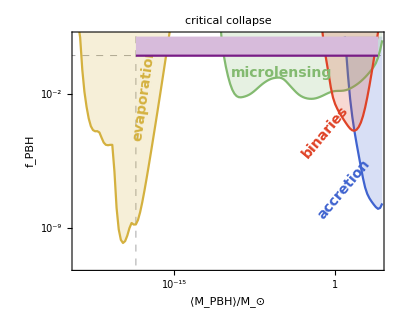

```mathematica
Show[ListPlot[{#[[1]],Log10[1/Max[1.*^-20,#[[2,1]]]]}&/@clist,Joined->True,PlotRange->{{-24,4},{-11,1}},Filling->Top,PlotStyle->ColorData["Rainbow"][0.2],PlotRangePadding->None,ImagePadding->{{58,4},{42,10}},GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"⟨M_PBH⟩/"<>Msunt,"f_PBH"},FrameTicks->{{logticksx,logticksx2},{logticksx3,logticksx4}},AspectRatio->0.8,ImageSize->400],
ListPlot[{#[[1]],Log10[1/Max[1.*^-20,Total[#[[2,2;;4]]]]]}&/@clist,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.5],None}],
ListPlot[{#[[1]],Log10[1/Max[1.*^-20,#[[2,5]]]]}&/@clist,Joined->True,Filling->Top,PlotStyle->ColorData["Rainbow"][0.95]],
ListPlot[{#[[1]],Log10[1/Max[1.*^-20,Total[#[[2,6;;9]]]]]}&/@clist,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.72],None}],
Plot[0,{x,Log10@Mevap,4},Filling->Top,PlotStyle->ColorData["Rainbow"][0.],FillingStyle->Opacity[1,Lighter[ColorData["Rainbow"][0.],0.7]]],Graphics[Text[Rotate[Style["evaporation",14,Bold,ColorData["Rainbow"][0.72]],82Degree],{-17.8,-2.}]],
Graphics[Text[Rotate[Style["microlensing",14,Bold,ColorData["Rainbow"][0.5]],0Degree],{-5.,-0.9}]],
Graphics[Text[Rotate[Style["binaries",14,Bold,ColorData["Rainbow"][0.95]],50Degree],{-0.9,-4.}]],
Graphics[Text[Rotate[Style["accretion",14,Bold,ColorData["Rainbow"][0.2]],50Degree],{0.8,-7.}]],
PlotLabel->Style["critical collapse",16]]
```